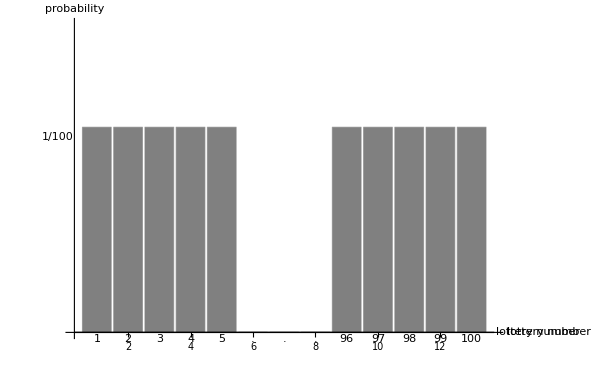

```mathematica
vX = Range[5];
vX1 = Table[".",{3}];
vX2 = Range[96,100,1];
vX = Join[vX,vX1,vX2];
vProbability = Table[1/100,{5}];
vProbability1 = Table[0,{3}];
vProbability2 = Table[1/100,{5}];
vProbability = Join[vProbability,vProbability1,vProbability2];
g1=Show[BarChart[vProbability,PlotRange->{Automatic,{0,0.015}},AxesLabel->{"lottery number ","probability "},ChartLabels->vX,Ticks ->{True,False},BaseStyle->{FontSize->16},ChartStyle->{Gray},Epilog->{Text["1/100",Scaled[{-0.02,.63}]]},ImagePadding->{{70,95},{30,30}}],ImageSize->600]
```

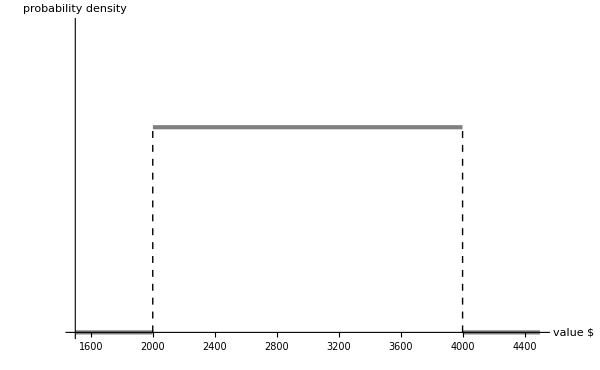

```mathematica
g2 = Show[Plot[PDF[UniformDistribution[{2000,4000}],θ],{θ,1500,4500},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{"value $ ","probability density "},Ticks->{True,False},PlotRange->{{1500,4500},{0,1.5*(1/2000)}},Epilog->{{Dashed,Line[{{2000,0},{2000,1/2000}}]},{Dashed,Line[{{4000,0},{4000,1/2000}}]}}],ImageSize->600,ImagePadding->{{70,95},{30,30}}]
```

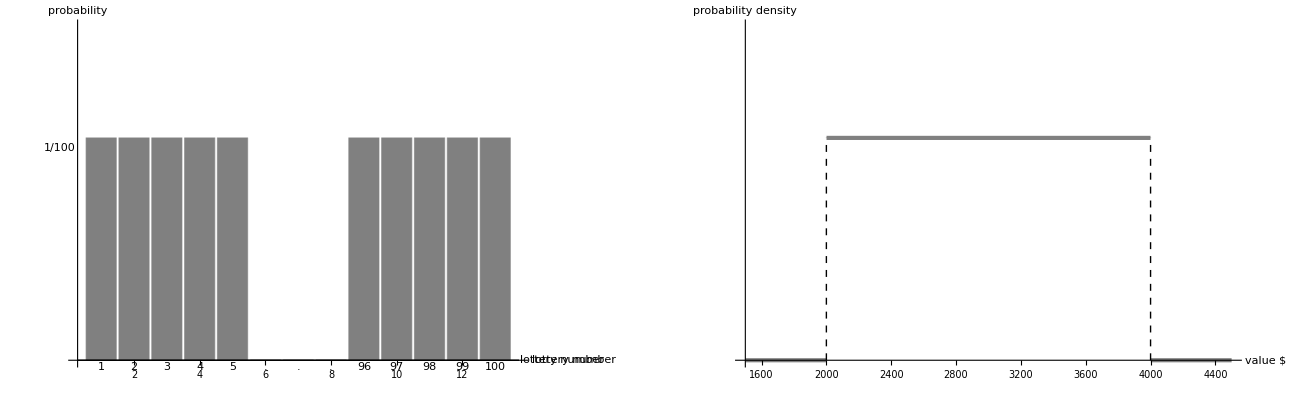

```mathematica
GraphicsRow[{g1,g2}]
```